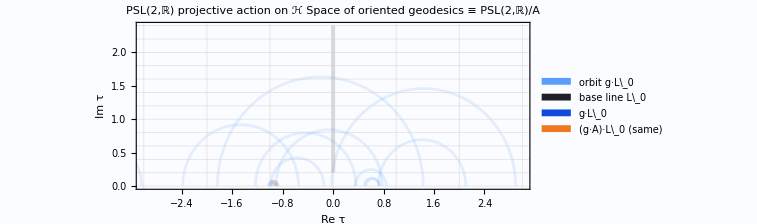

```mathematica
(* =================Base geometry& action=================*)ClearAll[mobPSL,geoEndpointsToCurve,verticalCurve,baseLine,Kmat,Nmat,Adiag,randKAN,imageEndpoints,geodesicOf,sameGeodesicQ];

(*Möbius action of g={{a,b},{c,d}} on z in upper half-plane*)
mobPSL[g_,z_]:=(g[[1,1]] z+g[[1,2]])/(g[[2,1]] z+g[[2,2]]);

(*Geodesic from real endpoints u<v (semicircle orthogonal to ℝ)*)
geoEndpointsToCurve[u_?NumericQ,v_?NumericQ,n_:240]:=Module[{c=(u+v)/2.,r=(v-u)/2.,θ=Subdivide[0,Pi,n]},Line[Transpose@{c+r Cos[θ],r Sin[θ]}]];

(*Vertical geodesic x=x0 (segment within a plotting window)*)
verticalCurve[x0_?NumericQ,yMin_:0.2,yMax_:2.4,n_:240]:=Line[Transpose@{ConstantArray[x0,n],Subdivide[yMin,yMax,n-1]}];

baseLine=verticalCurve[0];

(*Diagonal subgroup A (Iwasawa):Adiag[t]=diag(e^t,e^-t)*)
Adiag[t_]:={{Exp[t],0},{0,Exp[-t]}};


Kmat[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
Nmat[n_]:={{1,n},{0,1}};
randKAN[]:=Module[{θ,t,n},θ=RandomReal[{-Pi,Pi}];
t=RandomReal[{-1.2,1.2}];
n=RandomReal[{-2,2}];
Kmat[θ].Adiag[t].Nmat[n]];

(*Image of {0,∞} under g without doing ∞-arithmetic:g·0=b/d if d≠0,else ∞;g·∞=a/c if c≠0,else ∞*)
imageEndpoints[g_?MatrixQ]:=Module[{a,b,c,d,u,v},{a,b,c,d}=Flatten[g];
u=If[d==0,Infinity,N[b/d]];
v=If[c==0,Infinity,N[a/c]];
{u,v}];

(*Build geodesic curve in H from endpoints*)
geodesicOf[g_?MatrixQ]:=Module[{u,v},{u,v}=imageEndpoints[g];
Which[u===Infinity&&v===Infinity,Nothing,(*degenerate;won’t occur for det=1 real g*)u===Infinity,verticalCurve[v],v===Infinity,verticalCurve[u],True,geoEndpointsToCurve@@Sort@{u,v}]];

(*Coset test:g and g·A(t) represent the same oriented geodesic*)
sameGeodesicQ[g_?MatrixQ,t_:1.3,tol_:10^-9]:=Module[{u1,v1,u2,v2},{u1,v1}=imageEndpoints[g];
{u2,v2}=imageEndpoints[g.Adiag[t]];
And@@(If[#1===Infinity&&#2===Infinity,True,If[NumericQ[#1]&&NumericQ[#2],Abs[#1-#2]<tol,False]]&@@@Transpose[{Sort@{u1,v1},Sort@{u2,v2}}])];

(* =================Colors& styling=================*)

colOrbit=RGBColor[0.35,0.62,0.98];   (*light blue:many-orbit geodesics*)
colBase=RGBColor[0.12,0.12,0.16];   (*near-black:base line*)
colHi1=RGBColor[0.06,0.29,0.86];   (*deep blue:g·L0*)
colHi2=RGBColor[0.94,0.47,0.13];   (*orange:(g·A)·L0*)

bg=RGBColor[0.985,0.99,1.];
gridStyle=Directive[GrayLevel[.8,.6],AbsoluteThickness[0.5]];

(* =================Build the picture=================*)

SeedRandom[7];
elts=randKAN[]&/@Range[14];
gPick=elts[[3]];
tParam=1.3;

orbitGraphics=Show[Graphics[{(*a bunch of orbit geodesics g·L0*)Directive[colOrbit,Opacity[.15],AbsoluteThickness[2]],Table[geodesicOf[g],{g,elts}],(*base line x=0*)Directive[colBase,AbsoluteThickness[3]],baseLine,(*highlight a coset representative pair:same geodesic*)Directive[colHi1,AbsoluteThickness[4]],geodesicOf[gPick],Directive[colHi2,Dashed,AbsoluteThickness[4]],geodesicOf[gPick.Adiag[tParam]]},Frame->True,FrameStyle->Directive[GrayLevel[.25],AbsoluteThickness[1.2]],FrameLabel->(Style[#,13,GrayLevel[.2]]&/@{"Re τ","Im τ"}),PlotRange->{{-3,3},{0,2.4}},Background->bg,GridLines->{Range[-3,3],Range[0,2.4,.2]},GridLinesStyle->gridStyle,ImageSize->560],PlotLabel->Style["PSL(2,ℝ) projective action on \!\(\*StyleBox[\"ℋ\",FontSlant->\"Italic\"]\)\n"<>"Space of oriented geodesics ≡ PSL(2,ℝ)/A",14,colBase],PlotRangePadding->Scaled[.02]];

legend=SwatchLegend[{colOrbit,colBase,colHi1,colHi2},{"orbit  g·L\_0","base line  L\_0","g·L\_0","(g·A)·L\_0  (same)"},LegendLayout->"Column",LabelStyle->Directive[12,GrayLevel[.2]],LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->GrayLevel[.85]]&)];

Legended[orbitGraphics,Placed[legend,{Right,Bottom}]]
```